Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

alphaAngle: 1.2 , emissionAngle: π/6, inclinationAngle: 1.54355 , θ[0]: 0.523599 , θ[10000]: 2.06577

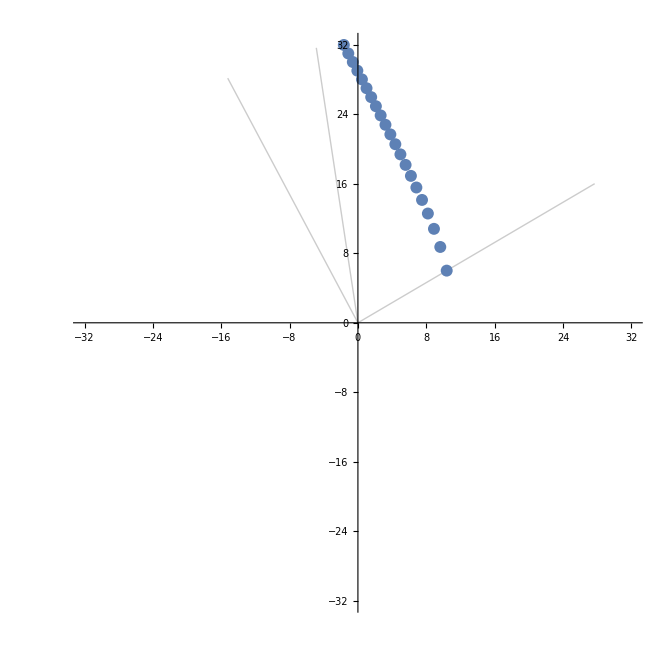

Time elapsed: 1.727002

Fields at z = 0: 0.

Fields at z = 50: 0.0000761196

Fields at z = 100: -0.0346376

bx at z = 100: 7.31731×10^9

by at z = 100: -2.53607×10^8

Ax = 0.739926, Ay = 0.00174925, φ = 0.258325

φ[100] = 0.0101197

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;
rg:=4.134;


(*Ray bending*)

alphaAngle:=1.2;
emissionAngle:=Pi/6;

b:=R0 Sin[alphaAngle]/Sqrt[1-rg/R0];

positiveDirection=True;

If[positiveDirection,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[3]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[2]];

,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[4]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[1]];]

Print["alphaAngle: ",alphaAngle," , emissionAngle: ",emissionAngle,", inclinationAngle: ",inclinationAngle," , θ[0]: ",trajectoryTheta/.z->0," , θ[10000]: ",trajectoryTheta/.z->10000];

(*Print[];
Print[];*)

zRange:=Range[0,20,1];
θRange:=trajectoryTheta/.z->zRange/.C[1]->0;

p0=ListPolarPlot[Transpose[{θRange,zRange+R0}],PlotRange->R0+Max[zRange],PolarGridLines->{{inclinationAngle+emissionAngle,alphaAngle+emissionAngle,emissionAngle},{}}]

(*Exit[];*)

(*Mixing*)

angleXi:=-Pi/6;
angleTheta:=trajectoryTheta;
angleGamma:=Pi/4;



bR:=Abs[fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta])];
bTheta:=Abs[gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta])];
bPhi:=Abs[gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma])];

fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/(z+R0);

cosRotation= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;

bRep={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;



k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

(*Параметры АЛП*)
ω0=10;
g=6*10^(-20);
mass=10^(-8);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(rg/R0))/(1-(rg/(z+R0)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*mass^2*(1/ω);

deltaQEDxx:=k0 delta M/2;
deltaQEDyy:=k0 delta n/2;
deltaQEDxy:=k0 delta P/2;
deltaQEDyx:=deltaQEDxy;

(*Матрица М*)
mat:={{  deltaQEDxx,deltaQEDxy,deltaMx    },
	{deltaQEDyx,deltaQEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[z_]:={{r11[z],r12[z],r13[z]},{r21[z],r22[z],r23[z]},{r31[z],r32[z],r33[z]}};


(*Список начальных условий*)
oMode=True;

If[oMode,
(*O-mode*)
rmat0:={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
,
(*X-mode*)
rmat0:={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
]


upperLimitSolve:=5000;
upperLimitPlot:=500;

eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].Abs[mat]-Abs[mat].rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];
(*eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];*)

(*Print[mat/.bRep/.z->100//MatrixForm];*)
Print["Time elapsed: ",AbsoluteTime[]-time];

Print["Fields at z = 0: ",(by/Sqrt[by^2+bx^2])/.bRep/.z->0];
Print["Fields at z = 50: ",(by/Sqrt[by^2+bx^2])/.bRep/.z->50];
Print["Fields at z = 100: ",(by/Sqrt[by^2+bx^2])/.bRep/.z->100];
Print["bx at z = 100: ",(bx)/.bRep/.z->100];
Print["by at z = 100: ",(by)/.bRep/.z->100];


Print["Ax = ",Re[r11[z]]/.eqs[[1]]/.z->upperLimitSolve,", Ay = ",Re[r22[z]]/.eqs[[1]]/.z->upperLimitSolve,", φ = ",Re[r33[z]]/.eqs[[1]]/.z->upperLimitSolve];

Print["φ[100] = ",Re[r33[z]]/.eqs[[1]]/.z->100];


p1=Plot[Re[Evaluate[{r11[z]+r22[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.05,1.05}},PlotTheme->"Scientific",PlotStyle->Orange, PlotLegends->Placed[LineLegend[{Directive[Orange]},{"|A_x|^2+|A_y|^2"},LegendMarkerSize->30,LabelStyle->{FontSize->14,FontFamily->Times}],{0.92,0.8}]];
(*p2=Plot[Re[Evaluate[{r22[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.1,1.05}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed}, PlotLegends->Placed[LineLegend[{Directive[Red,Dashed]},{Superscript["|A_y|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14,FontFamily->Times}],{0.92,0.8}]];*)
p3=Plot[Re[Evaluate[{r33[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.05,1.05}},PlotTheme->"Scientific",PlotStyle->{Blue,Dashed}, PlotLegends->Placed[LineLegend[{Directive[Blue,Dashed]},{Superscript["|φ|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14,FontFamily->Times}],{0.92,0.8}]];

(*Show[p1,p2,p3]*)
Show[p1,p3,FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["r, km",16],Style[Superscript[" | Amplitude | " ,2],16]}]



zSet=Range[1,upperLimitPlot-1,upperLimitPlot/500];
bSet=ArcTan[Abs[by/bx]]/.bRep/.z->zSet;
ASet=ArcTan[Sqrt[Abs[Re[Evaluate[r22[z]/r11[z]/.eqs]]]]]/.z->zSet;
(*bySet=-by/.bRep/.z->zSet;*)

dataToFile = Transpose[{zSet,bSet,ASet[[1]]}];

Export["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Mixing_data\\Angles_data.csv",dataToFile,"Table"];

bASet=bSet+ASet[[1]];

p4=ListLogPlot[{Transpose[{zSet,bSet}],Transpose[{zSet,ASet[[1]]}]},Joined->True,PlotRange->{{0,upperLimitPlot},{0.01,Automatic}},PlotTheme->"Scientific", PlotLegends->Placed[LineLegend[{{Blue},{Red}},{{"tan^-1(B_y/B_x)"},{"tan^-1(A_y/A_x)"}},LegendMarkerSize->30,LabelStyle->{FontSize->14,FontFamily->Times}],{0.92,0.8}],FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["r, km",16],Style["Angle , rad",16]},PlotStyle->{{Blue},{Red}},InterpolationOrder->3]
```

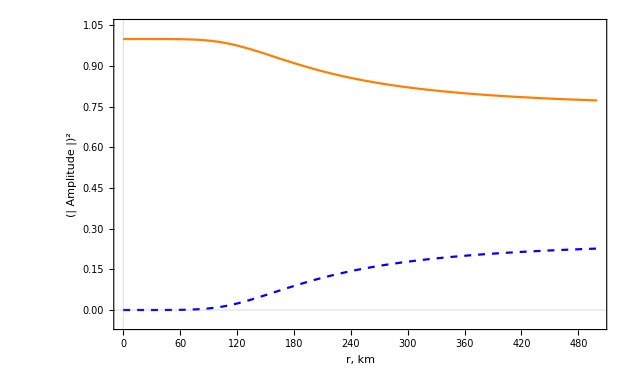

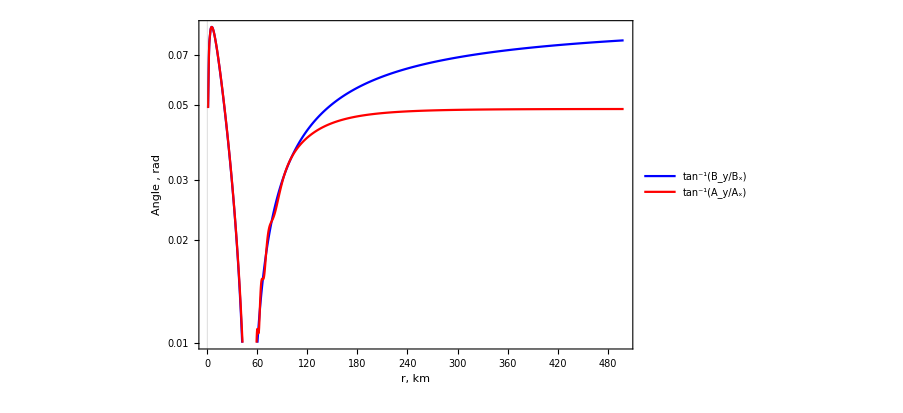

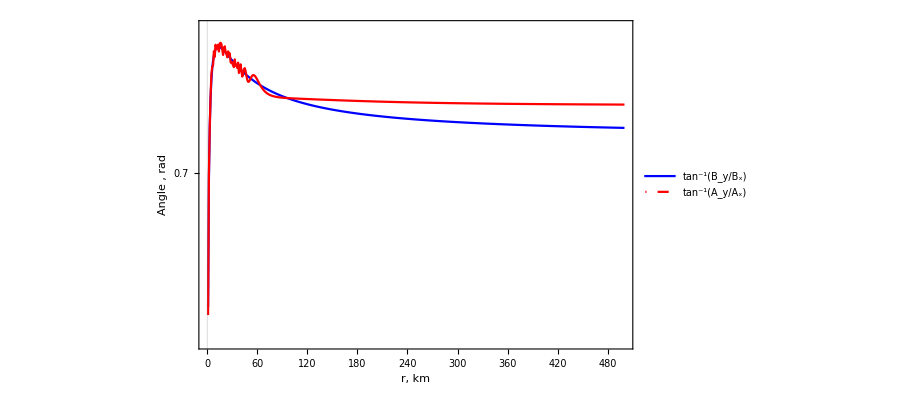

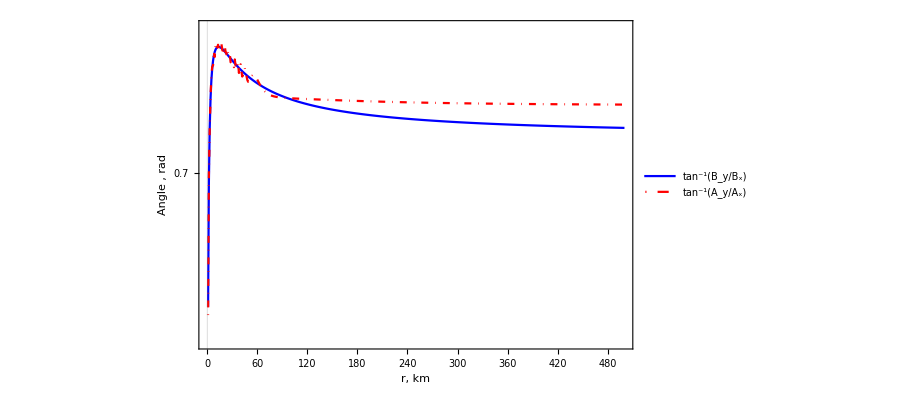

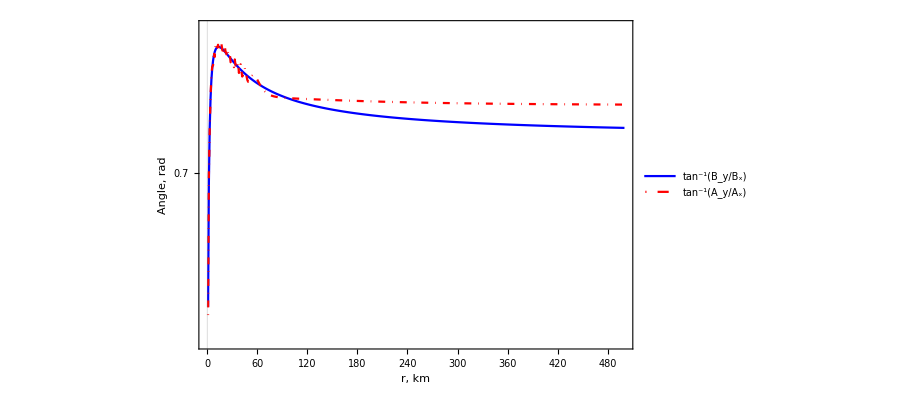

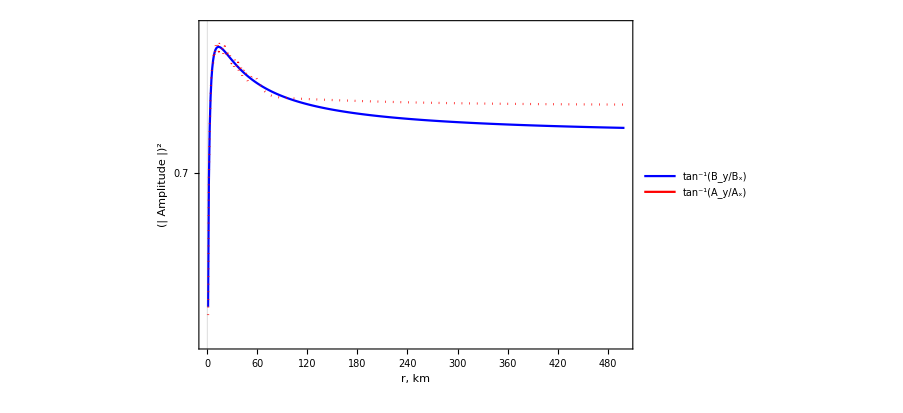

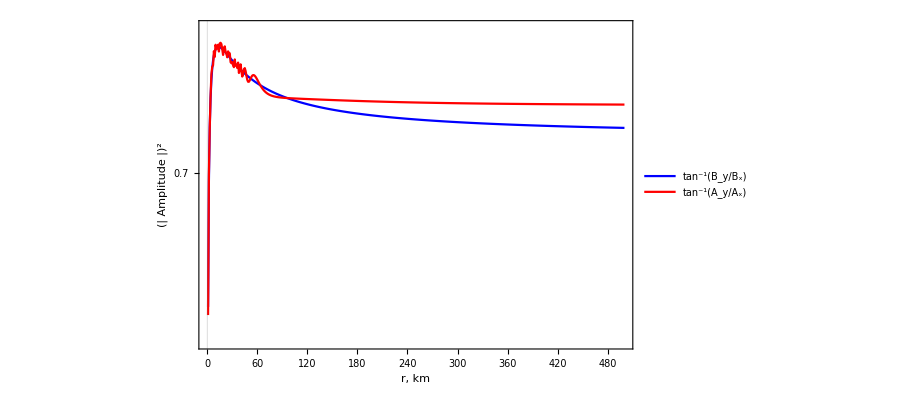

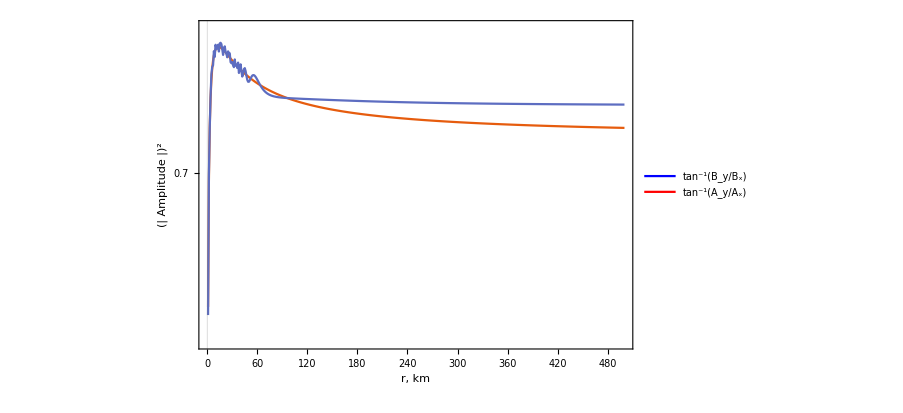

```mathematica
4.8*(BSurf/10^11)^(2/5)*(ω0/1000)^(1/5)
```

```mathematica
upperLimitPlot=200;
zSet=Range[50,upperLimitPlot,upperLimitPlot/50];

(*deltaMxSet=deltaMx/.bRep/.z->zSet;
deltaMySet=deltaMy/.bRep/.z->zSet;

deltaQEDxxSet=deltaQEDxx/.bRep/.z->zSet;
deltaQEDyySet=deltaQEDyy/.bRep/.z->zSet;*)
(*p4=ListLinePlot[{Transpose[{zSet,deltaMxSet}],Transpose[{zSet,deltaQEDxxSet}]},PlotLegends->{"deltaMx","deltaQEDxx"}]*)

probabilityXSet=4deltaMx^2/((deltaQEDxx+deltaMass)^2+4deltaMx^2)/.bRep/.z->zSet;
probabilityYSet=4deltaMy^2/((deltaQEDyy+deltaMass)^2+4deltaMy^2)/.bRep/.z->zSet;

oscLenXSet=z/(2Pi/Sqrt[(deltaQEDxx+deltaMass)^2+4deltaMx^2])/.bRep/.z->zSet;
oscLenYSet=0.4z/(2Pi/Sqrt[(deltaQEDyy+deltaMass)^2+4deltaMy^2])/.bRep/.z->zSet;

p4=ListLinePlot[{Transpose[{zSet,probabilityXSet}],Transpose[{zSet,probabilityYSet}]},PlotLegends->{"probabilityX","probabilityY"}]
p5=ListLinePlot[{Transpose[{zSet,oscLenXSet}],Transpose[{zSet,oscLenYSet}]},PlotLegends->{"oscLenX","oscLenY"}]
```

```mathematica
(*Positive Direction*)
```

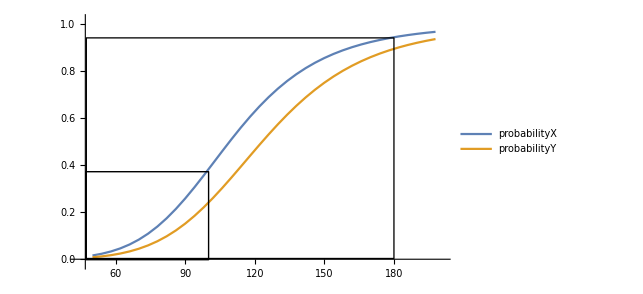

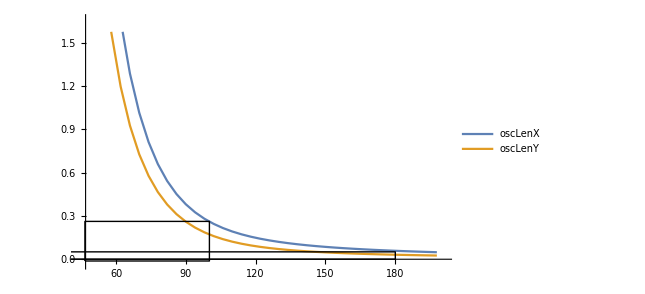

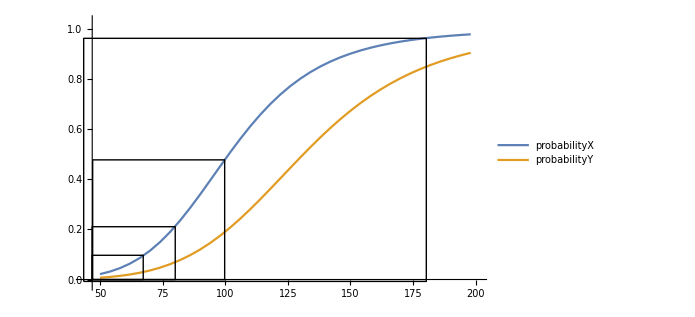
```mathematica
(*Negative direction*)
-Graphics-
```

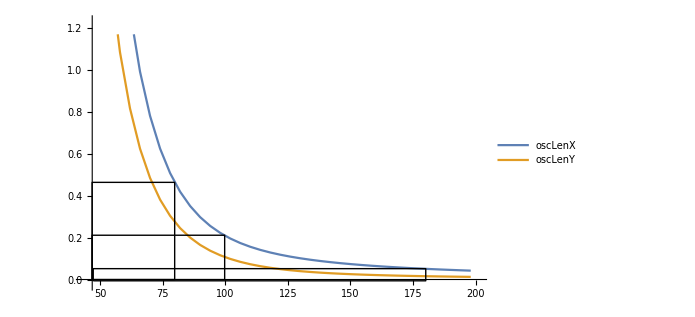

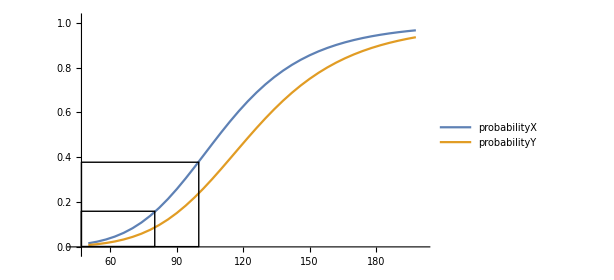
```mathematica
(*Positive direction*)
-Graphics-
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

alphaAngle: 1.0472 , emissionAngle: π/6, inclinationAngle: 1.33129 , θ[0]: 0.523599 , θ[10000]: 1.85361

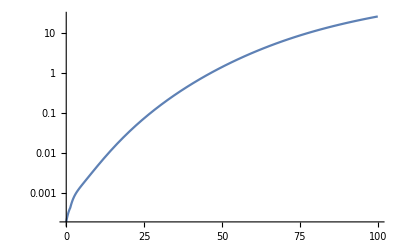

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;
rg:=4.134;


(*Ray bending*)

alphaAngle:=Pi/3.;
emissionAngle:=Pi/6;

b:=R0 Sin[alphaAngle]/Sqrt[1-rg/R0];

positiveDirection=True;

If[positiveDirection,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[3]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[2]];

,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[4]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[1]];]

Print["alphaAngle: ",alphaAngle," , emissionAngle: ",emissionAngle,", inclinationAngle: ",inclinationAngle," , θ[0]: ",trajectoryTheta/.z->0," , θ[10000]: ",trajectoryTheta/.z->10000];

(*Print[];
Print[];*)

zRange:=Range[0,20,1];
θRange:=trajectoryTheta/.z->zRange/.C[1]->0;

(*Exit[];*)

(*Mixing*)

angleXi:=Pi/4;
angleTheta:=trajectoryTheta;
angleGamma:=Pi/6;



bR:=Abs[fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta])];
bTheta:=Abs[gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta])];
bPhi:=Abs[gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma])];

fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/(z+R0);

cosRotation= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;

bRep={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;



k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

(*Параметры АЛП*)
ω0=1;
g=6*10^(-20);
mass=10^(-8);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(rg/R0))/(1-(rg/(z+R0)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*mass^2*(1/ω);

deltaQEDxx:=k0 delta M/2;
deltaQEDyy:=k0 delta n/2;
deltaQEDxy:=k0 delta P/2;
deltaQEDyx:=deltaQEDxy;

(*Матрица М*)
mat:={{  deltaQEDxx,deltaQEDxy,deltaMx    },
	{deltaQEDyx,deltaQEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[z_]:={{r11[z],r12[z],r13[z]},{r21[z],r22[z],r23[z]},{r31[z],r32[z],r33[z]}};


(*Список начальных условий*)
oMode=True;

If[oMode,
(*O-mode*)
rmat0:={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
,
(*X-mode*)
rmat0:={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
]


upperLimitSolve:=5000;
upperLimitPlot:=500;

(*LogPlot[{deltaQEDxx,deltaMx}/.bRep,{z,100,200}]
LogPlot[{Sqrt[deltaMy^2+deltaMx^2]}/.bRep,{z,0,100}]
LogPlot[{by}/.bRep,{z,0,10}]*)
LogPlot[{1/Sqrt[(deltaQEDyy^2+4deltaMy^2)]}/.bRep,{z,0,100}]
```